## Подготовка данных

```mathematica
SetDirectory@NotebookDirectory[];
{DataColumns=#⟦1⟧,Data=ReplaceAll[Select[#⟦2;;⟧,Last@#≠"Iris-versicolor"&],{"Iris-setosa"->0,"Iris-virginica"->1}]}&@Import["IRIS.csv","Data"];
Dimensions@#&/@%
{Data,DataLabels}={Data⟦All,;;4⟧,Data⟦All,5⟧};
```

{{5},{100,5}}

## Стандартизация данных

```mathematica
ClearAll[DataMin,DataMax,DataStd];
DataMin=Table[Min@Data⟦All,c⟧,{c,1,4}];
DataMax=Table[Max@Data⟦All,c⟧,{c,1,4}];
DataStd=Map[(#-DataMin)/(DataMax-DataMin)&,Data];
```

```mathematica
ClearAll[Train,Test];
{Train,Test}=Partition[RandomSample[Range@100],UpTo[IntegerPart[0.8*100]]];
```

```mathematica
ClearAll[setosa,virginica];
setosa=Intersection[Train,Flatten@Position[DataLabels,0]];
virginica=Intersection[Train,Flatten@Position[DataLabels,1]];
```

```mathematica
Fig0=ListPlot[{DataStd⟦setosa,{#1,#2}⟧,DataStd⟦virginica,{#1,#2}⟧},PlotLegends->{"setosa","virginica"},PlotStyle->{{Blue,Medium},{Red,Medium}},Frame->True,FrameLabel->{DataColumns⟦#1⟧,DataColumns⟦#2⟧}]&;
```

```mathematica
Manipulate[Fig0[x,y],{{x,1,"X"},1,4,1,SetterBar},{{y,3,"Y"},1,4,1,SetterBar}]
```

```mathematica
colors=Flatten[Table[{i,j}->ColorData["TemperatureMap",#⟦i,j⟧],{i,1,4},{j,1,4}]&@Correlation[DataStd],1];
Grid[Floor[Correlation[DataStd],0.001],ItemSize->{5,5},Background->{None,None,colors},Alignment->Center,Frame->All]
```

0.999 | -0.207 | 0.904 | 0.853
-0.207 | 1. | -0.479 | -0.446
0.904 | -0.479 | 1. | 0.969
0.853 | -0.446 | 0.969 | 1.

## Линейная регрессия. Начальное приближение

```mathematica
ClearAll[LinearLeastSquares];
(** 
Решение задачи M.a=b
M - матрица выборки (m×[n+1])
b - вектор-столбец ответов (m×1)
a - вектор-столбец искомых параметров ([n+1]×1)	
**)
LinearLeastSquares[M_,b_]:=Inverse[Transpose[M].M].(b.M)
```

```mathematica
ClearAll[Features];
Dimensions[Features=Transpose@Prepend[Transpose@DataStd⟦Train⟧,ConstantArray[1,Length@Train]]]
```

{80,5}

```mathematica
(** Сравнение со встроенной функцией Mathematica **)
LeastSquares[Features,DataLabels⟦Train⟧]
```

{0.0301282,-0.220117,-0.16308,1.02067,0.468469}

```mathematica
LinearLeastSquares[Features,DataLabels⟦Train⟧]
```

{0.0301282,-0.220117,-0.16308,1.02067,0.468469}

## Логистическая регрессия. Метод итеративного взвешенного МНК

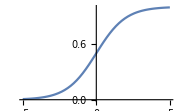

```mathematica
ClearAll[Sigma];
Sigma=Function[Z,1/(1+Exp[-Z])];
Plot[Sigma@x,{x,-5,5},ImageSize->Small]
```

Применяя алгоритм IRLS находим оптимальные параметры задачи:
Q(b)=∑_(i∈Samples) ln(1+σ(-y_iOverVector[x_i].b⃗))→min_b

```mathematica
ClearAll[b];
(** начальное приближение **)
b=Prepend[ConstantArray[0,Length@Data⟦1⟧],N@Log[#/(1-#)]&[Mean[DataLabels⟦Train⟧]]]
```

{0.0500104,0,0,0,0}

```mathematica
Dimensions[Z=Features.b]
Dimensions[p=Sigma[-Z]]
Dimensions[w=p*(1-p)];
W=DiagonalMatrix[w];
Dimensions[U=Z+(DataLabels⟦Train⟧-p)/w]
LinearLeastSquares[Transpose[Features].W.Features,Transpose[Features].W.U]
```

{80}

{80}

{80}

{-1.78062,-0.881018,-0.652729,4.08522,1.87505}

```mathematica
ClearAll[LogisticFitInit,LogisticFitStep];
LogisticFitInit[Features_,Answers_,n_]:=(
b=Prepend[ConstantArray[0,n],N@Log[#/(1-#)]&[Mean[Answers]]]
);
LogisticFitStep[Features_,Answers_]:=Block[{Z,p,w,W,U},
Z=Features.b;
p=Sigma[Z];
w=p*(1-p);
W=DiagonalMatrix[w];
U=Z+(Answers-p)/w;
LinearLeastSquares[Transpose[Features].W.Features,Transpose[Features].W.U]
]
LogisticFit[Features_,Answers_,iterations_]:=Block[{n,b,bNew,i,},
n=Length@Features⟦1⟧-1;
LogisticFitInit[Features,Answers,n];
For[i=1,i≤iterations,i++,
bNew=LogisticFitStep[Features,Answers];
Print[Norm[b-bNew]];
b=bNew;
];
Return@b;
]
```

```mathematica
LogisticFitInit[Features,DataLabels⟦Train⟧,4]
```

{0.0500104,0,0,0,0}

```mathematica
bNew=LogisticFitStep[Features,DataLabels⟦Train⟧]
```

{-1.88068,-0.881018,-0.652729,4.08522,1.87505}

```mathematica
Norm[bNew-b]
```

5.01345

```mathematica
ClearAll[weights];
weights=LogisticFit[Features,DataLabels⟦Train⟧,5]
```

5.01345

3.03316

2.87703

2.86291

2.89137

{-6.01765,-3.23311,-2.01676,13.9232,5.71583}

## Логистический классификатор

```mathematica
ClearAll[kmClassify];
kmClassify[X_]:=Sigma[weights.Prepend[X,1]]
```

```mathematica
Table[Round@kmClassify[X],{X,DataStd⟦Test⟧}]
DataLabels⟦Test⟧
```

{0,0,1,0,0,0,0,1,0,1,0,1,0,0,1,1,0,1,1,1}

{0,0,1,0,0,0,0,1,0,1,0,1,0,0,1,1,0,1,1,1}

## Визуализация

```mathematica
kmLine=ContourPlot[weights⟦#1⟧x+weights⟦#2⟧y+weights⟦1⟧==0,{x,-.5,1},{y,-.5,1},ContourStyle->Black]&;
```

```mathematica
Manipulate[Show[kmLine[x+1,y+1],Fig0[x,y]],{{x,3,"X"},1,4,1,SetterBar},{{y,4,"Y"},1,4,1,SetterBar}]
```